```mathematica
vars={{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}};
```

```mathematica
displacement=NDSolveValue[{SolidMechanicsPDEComponent[vars,pars]==SolidBoundaryLoadValue[x>=1/10,vars,pars,<|"Force"->{0,0,Quantity[-100, "Newtons"]}|>],
SolidFixedCondition[x<=-1/10,vars,pars]},{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}∈-Graphics3D-]
```

NDSolveValue::deqn: Equation or list of equations expected instead of SolidFixedCondition[x≤-1/10,{{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}},pars] in the first argument {SolidMechanicsPDEComponent[{{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}},pars]==SolidBoundaryLoadValue[x≥1/10,{{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}},pars,<|Force→{0,0,-}|>],SolidFixedCondition[«1»]}.

NDSolveValue[{SolidMechanicsPDEComponent[{{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}},pars]==SolidBoundaryLoadValue[x≥1/10,{{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}},pars,<|Force→{0,0,-100 N}|>],SolidFixedCondition[x≤-1/10,{{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}},pars]},{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}∈-Graphics3D-]

```mathematica
Entity["Element","Tungsten"]["PropertyAssociation"]
```

Lookup::invrl: The argument EntityValue[False,False,False] is not a valid Association or a list of rules.

Pick::incomp: Expressions {name,name,name,name,name,name,name,name,EntityProperty[EntityType,LabelPlural]} and {False,False,False,False,False,False,False,False,!Lookup[EntityFramework`Caching`Private`cacheData$69705,EntityProperty[EntityType,LabelPlural],False]} have incompatible shapes.

<|adiabatic index→Missing[NotApplicable],allotropes→{},allotropic multiplicities→{},alternate names→{wolfram},atomic mass→183.84 u,atomic number→74,atomic radius→193. pm,atomic symbol→W,block→d,boiling point→5555. °C,Brinell hardness→2570. MPa,bulk modulus→310. GPa,CAS number→CAS7440-33-7,color→Gray,common compound names→{tungsten(IV) selenide,tungsten(IV) telluride,sodium tungstate,sodium dodecatungstophosphate,copper(II) tungstate,tungsten trioxide,tungsten hexachloride,tungstic acid,phosphotungstic acid hydrate,tungsten hexacarbonyl,tungsten carbide,tungsten(IV) sulfide,calcium tungstate,tungsten(IV) chloride,tungsten(VI) oxychloride,tricarbonyl(mesitylene)tungsten(0),tungsten boride,ammonium tetrathiotungstate,barium tungstate,[1,2-bis(diphenylphosphino)ethane]tetracarbonyltungsten(0),ammonium metatungstate hydrate,silver tungstate,potassium tungstate,sodium metatungstate hydrate,sodium metatungstate,sodium tungstate dihydrate,tungsten(VI) dichloride dioxide,tungstosilicic acid hydrate,lead tungstate,tungsten(VI) fluoride,tungsten silicide,tungsten dioxide,tungsten(V) bromide,lithium tungstate,cadmium tungstate,barium calcium tungsten oxide,magnesium tungstate,barium strontium tungsten oxide,barium yttrium tungsten oxide,bis(cyclopentadienyl)tungsten(IV) dichloride,cesium tungstate,sodium phosphotungstate hydrate,ammonium tungstate,piperidine tetrathiotungstate,bis(cyclopentadienyl)tungsten(IV) dihydride,cyclopentadienyltungsten(II) tricarbonyl hydride,tetracarbonyl(1,5-cyclooctadiene)tungsten(0),tricarbonyl(1,3,5-cycloheptatriene)tungsten(0),bis(isopropylcyclopentadienyl)tungsten(IV) dihydride,bis(ethylcyclopentadienyl)tungsten(IV) dihydride,bis(butylcyclopentadienyl)tungsten(IV) dichloride,bis(butylcyclopentadienyl)tungsten(IV) dibromide,bis(butylcyclopentadienyl)tungsten(IV) diiodide,bis(cyclopentadienyl)tungsten(IV) chloride hydride,cerium(III) tungstate,bis(ethylcyclopentadienyl)tungsten(IV) dichloride,bis(isopropylcyclopentadienyl)tungsten(IV) dichloride,(propylcyclopentadienyl)tungsten(I) tricarbonyl dimer,dichlorobis(cyclopentadienyl)tungsten tetrafluoroborate,tungsten(0) pentacarbonyl-N-pentylisonitrile,tris(acetonitrile)tricarbonyltungsten(0),triamminetungsten(IV) tricarbonyl,cyclopentadienyltungsten(II) tricarbonyl chloride,(1,1'-bis(diphenylphosphino)ferrocene)tetracarbonyltungsten(0),bis(tert-butylimino)bis(dimethylamino)tungsten(VI),tris(tert-butoxy)(2,2-dimethylpropylidyne)tungsten(VI)},covalent radius→162. pm,critical pressure→Missing[NotAvailable],critical temperature→Missing[NotAvailable],crust abundance→0.00011  mass%,crust molar abundance→0.000012  mol%,Bravais lattice→body-centered cubic,lattice schematic→-Graphics3D-,Curie point→Missing[NotApplicable],Debye characteristic temperature→315 K,decay mode→Missing[NotApplicable],density→19.25 g/cm^3,discoverers→{Juan José D'Elhuyar,Fausto Elhuyar},discovery country→{Spain},discovery date→Year: 1783,electrical conductivity→2.×10^7 S/m,electrical type→conductors,electron affinity→78.6 kJ/mol,electron count→74,electronegativity→2.36,electronic configuration→1s^22s^22p^63s^23p^64s^23d^104p^65s^24d^105p^66s^24f^145d^4,electron shell configuration→{2,8,18,32,12,2},entity classes→{d-block elements,conductors,group 6 elements,metallic elements,naturally occurring elements,paramagnetic elements,period 6 elements,solid elements,stable elements,transition metals,merging neutron stars elements,dying low mass star elements},molar heat of fusion→35. kJ/mol,gas atomic multiplicities→Missing[NotApplicable],group→6,half-life→∞ s,human abundance→Missing[NotAvailable],human molar abundance→Missing[NotAvailable],icon color→RGBColor[0.681179, 0.360409, 0.63675],image→-Graphics-,ionization energies→{770. kJ/mol,1700. kJ/mol},isotope abundances→<|tungsten-180→0.12 %,tungsten-182→26.5 %,tungsten-183→14.31 %,tungsten-184→30.64 %,tungsten-186→28.43 %|>,isotope half-lives→<|tungsten-184→2.9×10^19 yr,tungsten-186→2.7×10^19 yr,tungsten-183→1.3×10^19 yr,tungsten-182→8.3×10^18 yr,tungsten-180→1.8×10^18 yr,tungsten-181→121.2 days,tungsten-185→75.1 days,tungsten-188→69.78 days,tungsten-178→21.6 days,tungsten-187→23.719 h,tungsten-176→150. min,tungsten-177→132. min,tungsten-179→37.05 min,tungsten-175→35.17 min,tungsten-174→33.17 min,tungsten-190→30. min,tungsten-189→10.7 min,tungsten-173→7.67 min,tungsten-172→6.7 min,tungsten-170→145. s,tungsten-171→143. s,tungsten-169→74. s,tungsten-168→53. s,tungsten-191→20. s,tungsten-167→19.9 s,tungsten-166→19.2 s,tungsten-192→10. s,tungsten-164→6.3 s,tungsten-165→5.1 s,tungsten-163→2.8 s,tungsten-162→1.36 s,tungsten-161→409. ms,tungsten-160→90. ms,tungsten-159→7.3 ms,tungsten-158→1.25 ms|>,isotope lifetimes→<|tungsten-184→4.2×10^19 yr,tungsten-186→3.9×10^19 yr,tungsten-183→1.9×10^19 yr,tungsten-182→1.2×10^19 yr,tungsten-180→2.6×10^18 yr,tungsten-181→174.9 days,tungsten-185→108. days,tungsten-188→100.7 days,tungsten-178→31.1 days,tungsten-187→34.22 h,tungsten-176→220. min,tungsten-177→190. min,tungsten-179→53.45 min,tungsten-175→50.83 min,tungsten-174→47.83 min,tungsten-190→43. min,tungsten-189→15.4 min,tungsten-173→11. min,tungsten-172→9.5 min,tungsten-170→209. s,tungsten-171→206. s,tungsten-169→110. s,tungsten-168→76. s,tungsten-191→29. s,tungsten-167→28.7 s,tungsten-166→27.7 s,tungsten-192→14. s,tungsten-164→9.1 s,tungsten-165→7.4 s,tungsten-163→4. s,tungsten-162→1.96 s,tungsten-161→590. ms,tungsten-160→130. ms,tungsten-159→11. ms,tungsten-158→1.8 ms|>,known isotopes→{tungsten-158,tungsten-159,tungsten-160,tungsten-161,tungsten-162,tungsten-163,tungsten-164,tungsten-165,tungsten-166,tungsten-167,tungsten-168,tungsten-169,tungsten-170,tungsten-171,tungsten-172,tungsten-173,tungsten-174,tungsten-175,tungsten-176,tungsten-177,tungsten-178,tungsten-179,tungsten-180,tungsten-181,tungsten-182,tungsten-183,tungsten-184,tungsten-185,tungsten-186,tungsten-187,tungsten-188,tungsten-189,tungsten-190,tungsten-191,tungsten-192},known oxidation states→{-2,-1,0,1,2,3,4,5,6},lattice angles→{90 °,90 °,90 °},lattice constants→{316.52 pm,316.52 pm,316.52 pm},Lewis structure→Missing[NotApplicable],liquid density→17.6 g/cm^3,magnetic type→paramagnetic elements,mass magnetic susceptibility→4.59×10^-9 m^3/kg,melting point→3422. °C,memberships→{d-block elements,conductors,group 6 elements,metallic elements,naturally occurring elements,paramagnetic elements,period 6 elements,solid elements,stable elements,transition metals,merging neutron stars elements,dying low mass star elements},meteorite abundance→0.000012  mass%,meteorite molar abundance→1.×10^-6  mol%,Mohs hardness→7.5,molar heat capacity→24. J/(mol K),molar magnetic susceptibility→8.44×10^-10 m^3/mol,molar mass→183.84 g/mol,molar radioactivity→Missing[NotApplicable],molar volume→9.55 cm^3/mol,most common oxidation states→{4,6},name→tungsten,Néel point→Missing[NotApplicable],number of neutrons per isotope→{tungsten-158→84,tungsten-159→85,tungsten-160→86,tungsten-161→87,tungsten-162→88,tungsten-163→89,tungsten-164→90,tungsten-165→91,tungsten-166→92,tungsten-167→93,tungsten-168→94,tungsten-169→95,tungsten-170→96,tungsten-171→97,tungsten-172→98,tungsten-173→99,tungsten-174→100,tungsten-175→101,tungsten-176→102,tungsten-177→103,tungsten-178→104,tungsten-179→105,tungsten-180→106,tungsten-181→107,tungsten-182→108,tungsten-183→109,tungsten-184→110,tungsten-185→111,tungsten-186→112,tungsten-187→113,tungsten-188→114,tungsten-189→115,tungsten-190→116,tungsten-191→117,tungsten-192→118},neutron cross-section→18.4 b,neutron mass absorption→0.0036 m^2/kg,nuclear diameter→Missing[NotAvailable],nuclear radius→Missing[NotAvailable],ocean abundance→1.2×10^-8  mass%,ocean molar abundance→4.×10^-10  mol%,orbital occupation list→{{2},{2,6},{2,6,10},{2,6,10,14},{2,6,4},{2}},origins→<|dying low mass star elements→57 %,merging neutron stars elements→43 %|>,period→6,phase at STP→solid,Poisson ratio→0.28,price→423.655 $,proton count→74,refractive index→Missing[NotAvailable],resistivity→5.×10^-8 m Ω,series→transition metals,shear modulus→161. GPa,short electronic configuration→[Xe]6s^24f^145d^4,solar abundance→4.×10^-7  mass%,solar molar abundance→3.×10^-9  mol%,molar heat of solidification→-35. kJ/mol,sound speed→5174. m/s,space group→crystallographic space group Im-3m,IUCr space group number→229,specific heat of fusion→0.2 kJ/g,specific heat at STP→132. J/(kg K),specific ionization energies→{4.2 kJ/g,9. kJ/g},specific radioactivity→Missing[NotApplicable],specific heat of solidification→-0.2 kJ/g,specific heat of vaporization→4. kJ/g,stable isotopes→{tungsten-180,tungsten-182,tungsten-183,tungsten-184,tungsten-186},superconducting point→0.015 K,tensile yield strength→750. MPa,term symbol→^5D_0,thermal conductivity→170. W/(m K),thermal expansion→4.5×10^-6 /K,threshold frequency→(1.×10^15to1.27×10^15) per second,ultimate tensile strength→0.98 GPa,universe abundance→5.×10^-8  mass%,universe molar abundance→3.×10^-10  mol%,unstable isotopes→{tungsten-158,tungsten-159,tungsten-160,tungsten-161,tungsten-162,tungsten-163,tungsten-164,tungsten-165,tungsten-166,tungsten-167,tungsten-168,tungsten-169,tungsten-170,tungsten-171,tungsten-172,tungsten-173,tungsten-174,tungsten-175,tungsten-176,tungsten-177,tungsten-178,tungsten-179,tungsten-181,tungsten-185,tungsten-187,tungsten-188,tungsten-189,tungsten-190,tungsten-191,tungsten-192},valence→6,number of valence electrons→2,van der Waals radius→Missing[NotAvailable],molar heat of vaporization→800. kJ/mol,Vickers hardness→3430. MPa,volume magnetic susceptibility→0.0000884,work function→(4.3to5.23) eV,Young modulus→411. GPa|>

```mathematica
CanonicalName/@Entity["Element","Tungsten"]["Properties"]
```

{AdiabaticIndex,AllotropeNames,AllotropicMultiplicities,AlternateNames,AtomicMass,AtomicNumber,AtomicRadius,AtomicSymbol,Block,BoilingPoint,BrinellHardness,BulkModulus,CASNumber,Color,CommonCompounds,CovalentRadius,CriticalPressure,CriticalTemperature,CrustAbundance,CrustMolarAbundance,CrystalStructure,CrystalStructureImage,CuriePoint,DebyeCharacteristicTemperature,DecayMode,Density,Discoverers,DiscoveryCountries,DiscoveryDate,ElectricalConductivity,ElectricalType,ElectronAffinity,ElectronCount,Electronegativity,ElectronicConfiguration,ElectronShellConfiguration,EntityClasses,FusionHeat,GasAtomicMultiplicities,Group,HalfLife,HumanAbundance,HumanMolarAbundance,IconColor,Image,IonizationEnergies,IsotopeAbundances,IsotopeHalfLives,IsotopeLifetimes,KnownIsotopes,KnownOxidationStates,LatticeAngles,LatticeConstants,LewisDotStructureDiagram,LiquidDensity,MagneticType,MassMagneticSusceptibility,MeltingPoint,Memberships,MeteoriteAbundance,MeteoriteMolarAbundance,MohsHardness,MolarHeatCapacity,MolarMagneticSusceptibility,MolarMass,MolarRadioactivity,MolarVolume,MostCommonOxidationStates,Name,NeelPoint,NeutronCount,NeutronCrossSection,NeutronMassAbsorption,NuclearDiameter,NuclearRadius,OceanAbundance,OceanMolarAbundance,OrbitalOccupationList,Origins,Period,Phase,PoissonRatio,Price,ProtonCount,RefractiveIndex,Resistivity,Series,ShearModulus,ShortElectronicConfiguration,SolarAbundance,SolarMolarAbundance,SolidificationHeat,SoundSpeed,SpaceGroup,SpaceGroupNumber,SpecificFusionHeat,SpecificHeat,SpecificIonizationEnergies,SpecificRadioactivity,SpecificSolidificationHeat,SpecificVaporizationHeat,StableIsotopes,SuperconductingPoint,TensileYieldStrength,TermSymbol,ThermalConductivity,ThermalExpansion,ThresholdFrequency,UltimateTensileStrength,UniverseAbundance,UniverseMolarAbundance,UnstableIsotopes,Valence,ValenceElectronCount,VanDerWaalsRadius,VaporizationHeat,VickersHardness,VolumeMagneticSusceptibility,WorkFunction,YoungModulus}

```mathematica
SolidMechanicsPDEComponentparamatersSpaceproperties={"MassDensity","Material","BulkModulus","LameParameter","PoissonRatio","ShearModulus","YoungModulus"}
```

{MassDensity,Material,BulkModulus,LameParameter,PoissonRatio,ShearModulus,YoungModulus}

```mathematica
Select[StringContainsQ[#,"Modulus"]&][CanonicalName/@Entity["Element","Tungsten"]["Properties"]]
```

{BulkModulus,ShearModulus,YoungModulus}

```mathematica
Select[StringContainsQ[#,"PoissonRatio"]&][CanonicalName/@Entity["Element","Tungsten"]["Properties"]]
```

{PoissonRatio}

```mathematica
Select[StringContainsQ[#,"LameParameter"]&][CanonicalName/@Entity["Element","Tungsten"]["Properties"]]
```

{}

```mathematica
tungstenProperties=AssociationMap[Entity["Element","Tungsten"][#]&,{"Density","BulkModulus","PoissonRatio","ShearModulus","YoungModulus"}]
```

<|Density→19.25 g/cm^3,BulkModulus→310. GPa,PoissonRatio→0.28,ShearModulus→161. GPa,YoungModulus→411. GPa|>

```mathematica
pars=<|"Density"->Quantity[19.25`5., ("Grams")/("Centimeters")^3],"BulkModulus"->Quantity[310.`3., "Gigapascals"],"PoissonRatio"->0.28`2.,"ShearModulus"->Quantity[161.`3., "Gigapascals"],"YoungModulus"->Quantity[411.`3., "Gigapascals"]|>
```

<|Density→19.25 g/cm^3,BulkModulus→310. GPa,PoissonRatio→0.28,ShearModulus→161. GPa,YoungModulus→411. GPa|>

```mathematica
displacement=NDSolveValue[{SolidMechanicsPDEComponent[vars,pars]==SolidBoundaryLoadValue[x>=1/10,vars,pars,<|"Force"->{0,0,Quantity[-100, "Newtons"]}|>],
SolidFixedCondition[x<=-1/10,vars,pars]},{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}∈-Graphics3D-]
```

{InterpolatingFunction[{{-0.106619, 0.177188}, {-0.0366367, 0.0245024}, {-0.0141908, 0.0372075}}, <>][x,y,z],InterpolatingFunction[{{-0.106619, 0.177188}, {-0.0366367, 0.0245024}, {-0.0141908, 0.0372075}}, <>][x,y,z],InterpolatingFunction[{{-0.106619, 0.177188}, {-0.0366367, 0.0245024}, {-0.0141908, 0.0372075}}, <>][x,y,z]}

```mathematica
AssociationMap[Entity["Element","Tungsten"][#]&,{"Density","BulkModulus","PoissonRatio","ShearModulus","YoungModulus"}]
```

```mathematica
EntityList/@{EntityClass["Element","Metal"],EntityClass["Element","TransitionMetal"]}
```

{{lithium,beryllium,sodium,magnesium,aluminum,potassium,calcium,scandium,titanium,vanadium,chromium,manganese,iron,cobalt,nickel,copper,zinc,gallium,arsenic,rubidium,strontium,yttrium,zirconium,niobium,molybdenum,technetium,ruthenium,rhodium,palladium,silver,cadmium,indium,tin,antimony,cesium,barium,lanthanum,cerium,praseodymium,neodymium,promethium,samarium,europium,gadolinium,terbium,dysprosium,holmium,erbium,thulium,ytterbium,lutetium,hafnium,tantalum,tungsten,rhenium,osmium,iridium,platinum,gold,mercury,thallium,lead,bismuth,polonium,francium,radium,actinium,thorium,protactinium,uranium,neptunium,plutonium,americium,curium,berkelium,californium,einsteinium,fermium,mendelevium,nobelium,lawrencium,rutherfordium,dubnium,seaborgium,bohrium,hassium,meitnerium,darmstadtium,roentgenium,copernicium,nihonium,flerovium,moscovium,livermorium},{scandium,titanium,vanadium,chromium,manganese,iron,cobalt,nickel,copper,zinc,yttrium,zirconium,niobium,molybdenum,technetium,ruthenium,rhodium,palladium,silver,cadmium,lutetium,hafnium,tantalum,tungsten,rhenium,osmium,iridium,platinum,gold,mercury,lawrencium,rutherfordium,dubnium,seaborgium,bohrium,hassium,meitnerium,darmstadtium,roentgenium,copernicium}}

```mathematica
Flatten[EntityList/@{EntityClass["Element","Metal"],EntityClass["Element","TransitionMetal"]}]
```

{lithium,beryllium,sodium,magnesium,aluminum,potassium,calcium,scandium,titanium,vanadium,chromium,manganese,iron,cobalt,nickel,copper,zinc,gallium,arsenic,rubidium,strontium,yttrium,zirconium,niobium,molybdenum,technetium,ruthenium,rhodium,palladium,silver,cadmium,indium,tin,antimony,cesium,barium,lanthanum,cerium,praseodymium,neodymium,promethium,samarium,europium,gadolinium,terbium,dysprosium,holmium,erbium,thulium,ytterbium,lutetium,hafnium,tantalum,tungsten,rhenium,osmium,iridium,platinum,gold,mercury,thallium,lead,bismuth,polonium,francium,radium,actinium,thorium,protactinium,uranium,neptunium,plutonium,americium,curium,berkelium,californium,einsteinium,fermium,mendelevium,nobelium,lawrencium,rutherfordium,dubnium,seaborgium,bohrium,hassium,meitnerium,darmstadtium,roentgenium,copernicium,nihonium,flerovium,moscovium,livermorium,scandium,titanium,vanadium,chromium,manganese,iron,cobalt,nickel,copper,zinc,yttrium,zirconium,niobium,molybdenum,technetium,ruthenium,rhodium,palladium,silver,cadmium,lutetium,hafnium,tantalum,tungsten,rhenium,osmium,iridium,platinum,gold,mercury,lawrencium,rutherfordium,dubnium,seaborgium,bohrium,hassium,meitnerium,darmstadtium,roentgenium,copernicium}

```mathematica
EntityValue[Flatten[EntityList/@{EntityClass["Element","Metal"],EntityClass["Element","TransitionMetal"]}],{"Density","BulkModulus","PoissonRatio","ShearModulus","YoungModulus"},"EntityPropertyAssociation"]
```

<|lithium→<|Density→0.535 g/cm^3,BulkModulus→11. GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→4.2 GPa,YoungModulus→4.9 GPa|>,beryllium→<|Density→1.848 g/cm^3,BulkModulus→130. GPa,PoissonRatio→0.032,ShearModulus→132. GPa,YoungModulus→287. GPa|>,sodium→<|Density→0.968 g/cm^3,BulkModulus→6.3 GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→3.3 GPa,YoungModulus→10. GPa|>,magnesium→<|Density→1.738 g/cm^3,BulkModulus→45. GPa,PoissonRatio→0.29,ShearModulus→17. GPa,YoungModulus→45. GPa|>,aluminum→<|Density→2.7 g/cm^3,BulkModulus→76. GPa,PoissonRatio→0.35,ShearModulus→26. GPa,YoungModulus→70. GPa|>,potassium→<|Density→0.856 g/cm^3,BulkModulus→3.1 GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→1.3 GPa,YoungModulus→Missing[NotAvailable]|>,calcium→<|Density→1.55 g/cm^3,BulkModulus→17. GPa,PoissonRatio→0.31,ShearModulus→7.4 GPa,YoungModulus→20. GPa|>,scandium→<|Density→2.985 g/cm^3,BulkModulus→57. GPa,PoissonRatio→0.28,ShearModulus→29. GPa,YoungModulus→74. GPa|>,titanium→<|Density→4.507 g/cm^3,BulkModulus→110. GPa,PoissonRatio→0.32,ShearModulus→44. GPa,YoungModulus→116. GPa|>,vanadium→<|Density→6.11 g/cm^3,BulkModulus→160. GPa,PoissonRatio→0.37,ShearModulus→47. GPa,YoungModulus→128. GPa|>,chromium→<|Density→7.19 g/cm^3,BulkModulus→160. GPa,PoissonRatio→0.21,ShearModulus→115. GPa,YoungModulus→279. GPa|>,manganese→<|Density→7.47 g/cm^3,BulkModulus→120. GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→198. GPa|>,iron→<|Density→7.874 g/cm^3,BulkModulus→170. GPa,PoissonRatio→0.29,ShearModulus→82. GPa,YoungModulus→211. GPa|>,cobalt→<|Density→8.9 g/cm^3,BulkModulus→180. GPa,PoissonRatio→0.31,ShearModulus→75. GPa,YoungModulus→209. GPa|>,nickel→<|Density→8.908 g/cm^3,BulkModulus→180. GPa,PoissonRatio→0.31,ShearModulus→76. GPa,YoungModulus→200. GPa|>,copper→<|Density→8.96 g/cm^3,BulkModulus→140. GPa,PoissonRatio→0.34,ShearModulus→48. GPa,YoungModulus→130. GPa|>,zinc→<|Density→7.14 g/cm^3,BulkModulus→70. GPa,PoissonRatio→0.25,ShearModulus→43. GPa,YoungModulus→108. GPa|>,gallium→<|Density→5.904 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,arsenic→<|Density→5.727 g/cm^3,BulkModulus→22. GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→8. GPa|>,rubidium→<|Density→1.532 g/cm^3,BulkModulus→2.5 GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→2.4 GPa|>,strontium→<|Density→2.63 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→0.28,ShearModulus→6.1 GPa,YoungModulus→Missing[NotAvailable]|>,yttrium→<|Density→4.472 g/cm^3,BulkModulus→41. GPa,PoissonRatio→0.24,ShearModulus→26. GPa,YoungModulus→64. GPa|>,zirconium→<|Density→6.511 g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→0.34,ShearModulus→33. GPa,YoungModulus→68. GPa|>,niobium→<|Density→8.57 g/cm^3,BulkModulus→170. GPa,PoissonRatio→0.4,ShearModulus→38. GPa,YoungModulus→105. GPa|>,molybdenum→<|Density→10.28 g/cm^3,BulkModulus→230. GPa,PoissonRatio→0.31,ShearModulus→120. GPa,YoungModulus→329. GPa|>,technetium→<|Density→11.5 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,ruthenium→<|Density→12.37 g/cm^3,BulkModulus→220. GPa,PoissonRatio→0.3,ShearModulus→173. GPa,YoungModulus→447. GPa|>,rhodium→<|Density→12.45 g/cm^3,BulkModulus→380. GPa,PoissonRatio→0.26,ShearModulus→150. GPa,YoungModulus→275. GPa|>,palladium→<|Density→12.023 g/cm^3,BulkModulus→180. GPa,PoissonRatio→0.39,ShearModulus→44. GPa,YoungModulus→121. GPa|>,silver→<|Density→10.49 g/cm^3,BulkModulus→100. GPa,PoissonRatio→0.37,ShearModulus→30. GPa,YoungModulus→83. GPa|>,cadmium→<|Density→8.65 g/cm^3,BulkModulus→42. GPa,PoissonRatio→0.3,ShearModulus→19. GPa,YoungModulus→50. GPa|>,indium→<|Density→7.31 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→11. GPa|>,tin→<|Density→7.31 g/cm^3,BulkModulus→58. GPa,PoissonRatio→0.36,ShearModulus→18. GPa,YoungModulus→50. GPa|>,antimony→<|Density→6.697 g/cm^3,BulkModulus→42. GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→20. GPa,YoungModulus→55. GPa|>,cesium→<|Density→1.879 g/cm^3,BulkModulus→1.6 GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→1.7 GPa|>,barium→<|Density→3.51 g/cm^3,BulkModulus→9.6 GPa,PoissonRatio→Missing[NotAvailable],ShearModulus→4.9 GPa,YoungModulus→13. GPa|>,lanthanum→<|Density→6.146 g/cm^3,BulkModulus→28. GPa,PoissonRatio→0.28,ShearModulus→14.3 GPa,YoungModulus→37. GPa|>,cerium→<|Density→6.689 g/cm^3,BulkModulus→22. GPa,PoissonRatio→0.24,ShearModulus→14. GPa,YoungModulus→34. GPa|>,praseodymium→<|Density→6.64 g/cm^3,BulkModulus→29. GPa,PoissonRatio→0.28,ShearModulus→15. GPa,YoungModulus→37. GPa|>,neodymium→<|Density→7.01 g/cm^3,BulkModulus→32. GPa,PoissonRatio→0.28,ShearModulus→16.3 GPa,YoungModulus→41. GPa|>,promethium→<|Density→7.264 g/cm^3,BulkModulus→33. GPa,PoissonRatio→0.28,ShearModulus→18. GPa,YoungModulus→46. GPa|>,samarium→<|Density→7.353 g/cm^3,BulkModulus→38. GPa,PoissonRatio→0.27,ShearModulus→20. GPa,YoungModulus→50. GPa|>,europium→<|Density→5.244 g/cm^3,BulkModulus→8.3 GPa,PoissonRatio→0.15,ShearModulus→7.9 GPa,YoungModulus→18. GPa|>,gadolinium→<|Density→7.901 g/cm^3,BulkModulus→38. GPa,PoissonRatio→0.26,ShearModulus→22. GPa,YoungModulus→55. GPa|>,terbium→<|Density→8.219 g/cm^3,BulkModulus→38.7 GPa,PoissonRatio→0.26,ShearModulus→22. GPa,YoungModulus→56. GPa|>,dysprosium→<|Density→8.551 g/cm^3,BulkModulus→41. GPa,PoissonRatio→0.25,ShearModulus→25. GPa,YoungModulus→61. GPa|>,holmium→<|Density→8.795 g/cm^3,BulkModulus→40. GPa,PoissonRatio→0.23,ShearModulus→26.3 GPa,YoungModulus→65. GPa|>,erbium→<|Density→9.066 g/cm^3,BulkModulus→44. GPa,PoissonRatio→0.24,ShearModulus→28. GPa,YoungModulus→70. GPa|>,thulium→<|Density→9.321 g/cm^3,BulkModulus→45. GPa,PoissonRatio→0.21,ShearModulus→31. GPa,YoungModulus→74. GPa|>,ytterbium→<|Density→6.57 g/cm^3,BulkModulus→31. GPa,PoissonRatio→0.21,ShearModulus→9.9 GPa,YoungModulus→24. GPa|>,lutetium→<|Density→9.841 g/cm^3,BulkModulus→48. GPa,PoissonRatio→0.26,ShearModulus→27. GPa,YoungModulus→69. GPa|>,hafnium→<|Density→13.31 g/cm^3,BulkModulus→110. GPa,PoissonRatio→0.37,ShearModulus→30. GPa,YoungModulus→78. GPa|>,tantalum→<|Density→16.65 g/cm^3,BulkModulus→200. GPa,PoissonRatio→0.34,ShearModulus→69. GPa,YoungModulus→186. GPa|>,tungsten→<|Density→19.25 g/cm^3,BulkModulus→310. GPa,PoissonRatio→0.28,ShearModulus→161. GPa,YoungModulus→411. GPa|>,rhenium→<|Density→21.02 g/cm^3,BulkModulus→370. GPa,PoissonRatio→0.3,ShearModulus→178. GPa,YoungModulus→463. GPa|>,osmium→<|Density→22.59 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→0.25,ShearModulus→222. GPa,YoungModulus→Missing[NotAvailable]|>,iridium→<|Density→22.56 g/cm^3,BulkModulus→320. GPa,PoissonRatio→0.26,ShearModulus→210. GPa,YoungModulus→528. GPa|>,platinum→<|Density→21.45 g/cm^3,BulkModulus→230. GPa,PoissonRatio→0.38,ShearModulus→61. GPa,YoungModulus→168. GPa|>,gold→<|Density→19.3 g/cm^3,BulkModulus→220. GPa,PoissonRatio→0.44,ShearModulus→27. GPa,YoungModulus→78. GPa|>,mercury→<|Density→13.534 g/cm^3,BulkModulus→25. GPa,PoissonRatio→Missing[NotApplicable],ShearModulus→Missing[NotApplicable],YoungModulus→Missing[NotApplicable]|>,thallium→<|Density→11.85 g/cm^3,BulkModulus→43. GPa,PoissonRatio→0.45,ShearModulus→2.8 GPa,YoungModulus→8. GPa|>,lead→<|Density→11.34 g/cm^3,BulkModulus→46. GPa,PoissonRatio→0.44,ShearModulus→5.6 GPa,YoungModulus→16. GPa|>,bismuth→<|Density→9.78 g/cm^3,BulkModulus→31. GPa,PoissonRatio→0.33,ShearModulus→12. GPa,YoungModulus→32. GPa|>,polonium→<|Density→9.196 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,francium→<|Density→2.9 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,radium→<|Density→5. g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,actinium→<|Density→10.07 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,thorium→<|Density→11.724 g/cm^3,BulkModulus→54. GPa,PoissonRatio→0.27,ShearModulus→31. GPa,YoungModulus→79. GPa|>,protactinium→<|Density→15.37 g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→Missing[Unknown],ShearModulus→Missing[Unknown],YoungModulus→Missing[Unknown]|>,uranium→<|Density→19.05 g/cm^3,BulkModulus→100. GPa,PoissonRatio→0.23,ShearModulus→111. GPa,YoungModulus→208. GPa|>,neptunium→<|Density→20.45 g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→Missing[Unknown],ShearModulus→Missing[Unknown],YoungModulus→Missing[Unknown]|>,plutonium→<|Density→19.816 g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→0.21,ShearModulus→43. GPa,YoungModulus→96. GPa|>,americium→<|Density→13.67 g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→Missing[Unknown],ShearModulus→Missing[Unknown],YoungModulus→Missing[Unknown]|>,curium→<|Density→13.51 g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→Missing[Unknown],ShearModulus→Missing[Unknown],YoungModulus→Missing[Unknown]|>,berkelium→<|Density→14.78 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,californium→<|Density→15.1 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,einsteinium→<|Density→8.84 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,fermium→<|Density→9.71 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,mendelevium→<|Density→10.37 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,nobelium→<|Density→9.94 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,lawrencium→<|Density→15.6 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,rutherfordium→<|Density→23.2 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,dubnium→<|Density→29.3 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,seaborgium→<|Density→35.3 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,bohrium→<|Density→37.1 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,hassium→<|Density→41. g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,meitnerium→<|Density→37.4 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,darmstadtium→<|Density→34.8 g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→Missing[Unknown],ShearModulus→Missing[Unknown],YoungModulus→Missing[Unknown]|>,roentgenium→<|Density→28.7 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,copernicium→<|Density→14. g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,nihonium→<|Density→16. g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→Missing[Unknown],ShearModulus→Missing[Unknown],YoungModulus→Missing[Unknown]|>,flerovium→<|Density→14. g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,moscovium→<|Density→13.5 g/cm^3,BulkModulus→Missing[NotAvailable],PoissonRatio→Missing[NotAvailable],ShearModulus→Missing[NotAvailable],YoungModulus→Missing[NotAvailable]|>,livermorium→<|Density→12.9 g/cm^3,BulkModulus→Missing[Unknown],PoissonRatio→Missing[Unknown],ShearModulus→Missing[Unknown],YoungModulus→Missing[Unknown]|>|>

```mathematica
Dataset[EntityValue[Flatten[EntityList/@{EntityClass["Element","Metal"],EntityClass["Element","TransitionMetal"]}],{"Density","BulkModulus","PoissonRatio","ShearModulus","YoungModulus"},"EntityPropertyAssociation"]]
```

```mathematica
pars=<|"Density"->Quantity[19.25`5., ("Grams")/("Centimeters")^3]|>
```

```mathematica
displacement=NDSolveValue[{SolidMechanicsPDEComponent[vars,pars]==SolidBoundaryLoadValue[x>=1/10,vars,pars,<|"Force"->{0,0,Quantity[-100, "Newtons"]}|>],
SolidFixedCondition[x<=-1/10,vars,pars]},{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}∈-Graphics3D-]
```

{InterpolatingFunction[{{-0.106619, 0.177188}, {-0.0366367, 0.0245024}, {-0.0141908, 0.0372075}}, <>][x,y,z],InterpolatingFunction[{{-0.106619, 0.177188}, {-0.0366367, 0.0245024}, {-0.0141908, 0.0372075}}, <>][x,y,z],InterpolatingFunction[{{-0.106619, 0.177188}, {-0.0366367, 0.0245024}, {-0.0141908, 0.0372075}}, <>][x,y,z]}

```mathematica
VectorDisplacementPlot3D[displacement,{x,y,z}∈-Graphics3D-]
```

-Graphics3D-

```mathematica
strains=SolidMechanicsStrain[vars,pars,displacement]
```

SymmetrizedArray[{3, 3}, <6,Symmetric[{1, 2}]>]

```mathematica
FindMaximum[{strains[[3,3]],{x,y,z}∈-Graphics3D-},{x,y,z}]
```

FindMinimum::nrnum: The function value Indeterminate is not a real number at {x,y,z} = {-0.100272,-0.0129215,0.0297618}.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {x,y,z} = {-0.100388,-0.0129215,0.0297618}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

{0.000110563,{x→-0.100266,y→-0.0129215,z→0.0297618}}

```mathematica
RandomPoint[-Graphics3D-,3]
```

{{-0.0123566,-0.000896923,0.0173457},{-0.0077058,0.00459651,0.0143834},{-0.0918348,-0.0110235,0.0280461}}

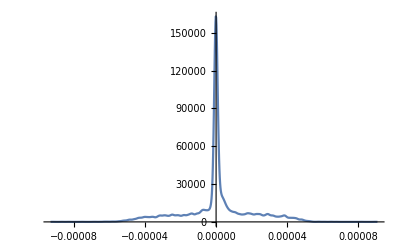

```mathematica
SmoothHistogram[Function[{x,y,z},Evaluate[strains[[3,3]]]]@@@RandomPoint[-Graphics3D-,10000],PlotRange->All]
```